# Omicron US analysis: Plotting partitioned case counts

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={"California","Colorado","North Carolina"};
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-10-15","2021-11-01","2021-11-15","2021-12-01","2021-12-15","2022-01-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-15

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-01-01

```mathematica
states=Union[seqData[[All,2]]]
```

{Arizona,California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Kentucky,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{Arizona,Connecticut,Florida,Georgia,Illinois,Indiana,Kentucky,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Jersey,New Mexico,New York,North Dakota,Ohio,Oregon,Pennsylvania,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
stateVariantCounts[state_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==state&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
stateSequenceCounts[state_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==state][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->stateSequenceCounts[#][[-15;;-1]]&,states]
```

{Arizona→{{2021-12-18,135},{2021-12-19,76},{2021-12-20,225},{2021-12-21,267},{2021-12-22,285},{2021-12-23,228},{2021-12-24,27},{2021-12-25,18},{2021-12-26,25},{2021-12-27,165},{2021-12-28,318},{2021-12-29,66},{2021-12-30,163},{2021-12-31,71},{2022-01-01,48}},Connecticut→{{2021-12-18,94},{2021-12-19,97},{2021-12-20,198},{2021-12-21,202},{2021-12-22,247},{2021-12-23,195},{2021-12-24,88},{2021-12-25,7},{2021-12-26,95},{2021-12-27,196},{2021-12-28,167},{2021-12-29,193},{2021-12-30,27},{2021-12-31,1},{2022-01-01,0}},Florida→{{2021-12-18,253},{2021-12-19,169},{2021-12-20,318},{2021-12-21,448},{2021-12-22,507},{2021-12-23,225},{2021-12-24,12},{2021-12-25,13},{2021-12-26,355},{2021-12-27,157},{2021-12-28,161},{2021-12-29,38},{2021-12-30,0},{2021-12-31,0},{2022-01-01,13}},Georgia→{{2021-12-18,144},{2021-12-19,141},{2021-12-20,286},{2021-12-21,238},{2021-12-22,231},{2021-12-23,108},{2021-12-24,16},{2021-12-25,9},{2021-12-26,181},{2021-12-27,155},{2021-12-28,105},{2021-12-29,25},{2021-12-30,0},{2021-12-31,0},{2022-01-01,0}},Illinois→{{2021-12-18,119},{2021-12-19,191},{2021-12-20,293},{2021-12-21,266},{2021-12-22,389},{2021-12-23,211},{2021-12-24,26},{2021-12-25,15},{2021-12-26,171},{2021-12-27,167},{2021-12-28,65},{2021-12-29,34},{2021-12-30,61},{2021-12-31,32},{2022-01-01,18}},Indiana→{{2021-12-18,108},{2021-12-19,57},{2021-12-20,83},{2021-12-21,71},{2021-12-22,88},{2021-12-23,165},{2021-12-24,0},{2021-12-25,0},{2021-12-26,38},{2021-12-27,94},{2021-12-28,40},{2021-12-29,21},{2021-12-30,0},{2021-12-31,0},{2022-01-01,0}},Kentucky→{{2021-12-18,41},{2021-12-19,27},{2021-12-20,16},{2021-12-21,35},{2021-12-22,15},{2021-12-23,62},{2021-12-24,10},{2021-12-25,0},{2021-12-26,57},{2021-12-27,5},{2021-12-28,2},{2021-12-29,1},{2021-12-30,0},{2021-12-31,0},{2022-01-01,0}},Louisiana→{{2021-12-18,58},{2021-12-19,24},{2021-12-20,113},{2021-12-21,107},{2021-12-22,85},{2021-12-23,74},{2021-12-24,37},{2021-12-25,3},{2021-12-26,34},{2021-12-27,68},{2021-12-28,184},{2021-12-29,44},{2021-12-30,16},{2021-12-31,1},{2022-01-01,0}},Maryland→{{2021-12-18,78},{2021-12-19,81},{2021-12-20,174},{2021-12-21,331},{2021-12-22,182},{2021-12-23,107},{2021-12-24,63},{2021-12-25,85},{2021-12-26,85},{2021-12-27,62},{2021-12-28,44},{2021-12-29,34},{2021-12-30,37},{2021-12-31,25},{2022-01-01,25}},Massachusetts→{{2021-12-18,415},{2021-12-19,504},{2021-12-20,789},{2021-12-21,1076},{2021-12-22,607},{2021-12-23,421},{2021-12-24,8},{2021-12-25,5},{2021-12-26,634},{2021-12-27,1168},{2021-12-28,653},{2021-12-29,1370},{2021-12-30,1170},{2021-12-31,63},{2022-01-01,152}},Michigan→{{2021-12-18,80},{2021-12-19,109},{2021-12-20,145},{2021-12-21,143},{2021-12-22,146},{2021-12-23,102},{2021-12-24,8},{2021-12-25,8},{2021-12-26,60},{2021-12-27,107},{2021-12-28,51},{2021-12-29,20},{2021-12-30,21},{2021-12-31,16},{2022-01-01,0}},Minnesota→{{2021-12-18,42},{2021-12-19,108},{2021-12-20,69},{2021-12-21,66},{2021-12-22,59},{2021-12-23,63},{2021-12-24,28},{2021-12-25,23},{2021-12-26,22},{2021-12-27,13},{2021-12-28,4},{2021-12-29,10},{2021-12-30,13},{2021-12-31,12},{2022-01-01,3}},Nebraska→{{2021-12-18,28},{2021-12-19,19},{2021-12-20,70},{2021-12-21,37},{2021-12-22,15},{2021-12-23,10},{2021-12-24,20},{2021-12-25,16},{2021-12-26,28},{2021-12-27,112},{2021-12-28,139},{2021-12-29,100},{2021-12-30,15},{2021-12-31,2},{2022-01-01,4}},Nevada→{{2021-12-18,36},{2021-12-19,94},{2021-12-20,88},{2021-12-21,98},{2021-12-22,123},{2021-12-23,30},{2021-12-24,7},{2021-12-25,2},{2021-12-26,5},{2021-12-27,186},{2021-12-28,20},{2021-12-29,3},{2021-12-30,0},{2021-12-31,0},{2022-01-01,0}},New Jersey→{{2021-12-18,64},{2021-12-19,127},{2021-12-20,121},{2021-12-21,661},{2021-12-22,913},{2021-12-23,242},{2021-12-24,21},{2021-12-25,3},{2021-12-26,51},{2021-12-27,50},{2021-12-28,16},{2021-12-29,2},{2021-12-30,1},{2021-12-31,0},{2022-01-01,3}},New Mexico→{{2021-12-18,30},{2021-12-19,21},{2021-12-20,29},{2021-12-21,37},{2021-12-22,42},{2021-12-23,34},{2021-12-24,12},{2021-12-25,5},{2021-12-26,9},{2021-12-27,12},{2021-12-28,17},{2021-12-29,16},{2021-12-30,19},{2021-12-31,11},{2022-01-01,20}},New York→{{2021-12-18,538},{2021-12-19,397},{2021-12-20,717},{2021-12-21,504},{2021-12-22,599},{2021-12-23,665},{2021-12-24,179},{2021-12-25,72},{2021-12-26,50},{2021-12-27,233},{2021-12-28,108},{2021-12-29,41},{2021-12-30,0},{2021-12-31,0},{2022-01-01,4}},North Dakota→{{2021-12-18,17},{2021-12-19,28},{2021-12-20,37},{2021-12-21,94},{2021-12-22,58},{2021-12-23,118},{2021-12-24,21},{2021-12-25,9},{2021-12-26,20},{2021-12-27,57},{2021-12-28,125},{2021-12-29,28},{2021-12-30,69},{2021-12-31,18},{2022-01-01,1}},Ohio→{{2021-12-18,116},{2021-12-19,135},{2021-12-20,262},{2021-12-21,268},{2021-12-22,233},{2021-12-23,97},{2021-12-24,1},{2021-12-25,0},{2021-12-26,50},{2021-12-27,38},{2021-12-28,11},{2021-12-29,1},{2021-12-30,83},{2021-12-31,0},{2022-01-01,0}},Oregon→{{2021-12-18,18},{2021-12-19,38},{2021-12-20,44},{2021-12-21,90},{2021-12-22,60},{2021-12-23,63},{2021-12-24,18},{2021-12-25,12},{2021-12-26,28},{2021-12-27,36},{2021-12-28,39},{2021-12-29,46},{2021-12-30,15},{2021-12-31,15},{2022-01-01,5}},Pennsylvania→{{2021-12-18,106},{2021-12-19,43},{2021-12-20,96},{2021-12-21,108},{2021-12-22,161},{2021-12-23,162},{2021-12-24,27},{2021-12-25,0},{2021-12-26,33},{2021-12-27,39},{2021-12-28,51},{2021-12-29,17},{2021-12-30,0},{2021-12-31,0},{2022-01-01,0}},Tennessee→{{2021-12-18,73},{2021-12-19,82},{2021-12-20,65},{2021-12-21,96},{2021-12-22,57},{2021-12-23,85},{2021-12-24,10},{2021-12-25,8},{2021-12-26,37},{2021-12-27,94},{2021-12-28,9},{2021-12-29,1},{2021-12-30,0},{2021-12-31,0},{2022-01-01,0}},Texas→{{2021-12-18,508},{2021-12-19,292},{2021-12-20,555},{2021-12-21,606},{2021-12-22,659},{2021-12-23,288},{2021-12-24,19},{2021-12-25,0},{2021-12-26,216},{2021-12-27,188},{2021-12-28,214},{2021-12-29,6},{2021-12-30,0},{2021-12-31,0},{2022-01-01,1}},Utah→{{2021-12-18,118},{2021-12-19,94},{2021-12-20,153},{2021-12-21,103},{2021-12-22,113},{2021-12-23,74},{2021-12-24,0},{2021-12-25,0},{2021-12-26,24},{2021-12-27,242},{2021-12-28,239},{2021-12-29,246},{2021-12-30,33},{2021-12-31,0},{2022-01-01,0}},Vermont→{{2021-12-18,47},{2021-12-19,27},{2021-12-20,10},{2021-12-21,7},{2021-12-22,4},{2021-12-23,0},{2021-12-24,0},{2021-12-25,0},{2021-12-26,35},{2021-12-27,58},{2021-12-28,5},{2021-12-29,25},{2021-12-30,3},{2021-12-31,0},{2022-01-01,0}},Virginia→{{2021-12-18,17},{2021-12-19,13},{2021-12-20,30},{2021-12-21,138},{2021-12-22,111},{2021-12-23,38},{2021-12-24,1},{2021-12-25,1},{2021-12-26,13},{2021-12-27,5},{2021-12-28,4},{2021-12-29,1},{2021-12-30,0},{2021-12-31,0},{2022-01-01,0}},Washington→{{2021-12-18,210},{2021-12-19,134},{2021-12-20,232},{2021-12-21,275},{2021-12-22,178},{2021-12-23,87},{2021-12-24,202},{2021-12-25,4},{2021-12-26,54},{2021-12-27,153},{2021-12-28,187},{2021-12-29,89},{2021-12-30,47},{2021-12-31,4},{2022-01-01,1}},Wisconsin→{{2021-12-18,114},{2021-12-19,108},{2021-12-20,225},{2021-12-21,205},{2021-12-22,234},{2021-12-23,187},{2021-12-24,61},{2021-12-25,11},{2021-12-26,91},{2021-12-27,114},{2021-12-28,38},{2021-12-29,2},{2021-12-30,190},{2021-12-31,87},{2022-01-01,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[state_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==state,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.0001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{logitTransform[logitMinFreq],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{0,If[maxFreq>0.95,1,maxFreq]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[state_]:=Map[logisticPrevSeries[stateVariantCounts[state,#],stateSequenceCounts[state]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForStates=Map[freqForCountry,states];
```

```mathematica
modeledFreqsForStates=Map[{modeledLogisticPrevSeries[logisticPrevSeries[stateVariantCounts[#,"Omicron"],stateSequenceCounts[#]]]}&,states];
```

```mathematica
legendsForStates=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForStates];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[state_,variant_]:=Module[{stateVariantFrequencyDateSeries,stateCasesDateSeries,tuples},
stateVariantFrequencyDateSeries=smoothedPrevalence[stateVariantCounts[state,variant],stateSequenceCounts[state]];
stateCasesDateSeries=csGather[state];
tuples=compareWithDate[stateVariantFrequencyDateSeries,stateCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

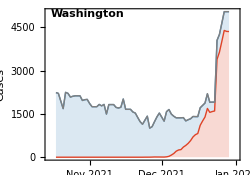

```mathematica
splitCasePlot["Washington"]
```

```mathematica
panels=Map[splitCasePlot,states];
```

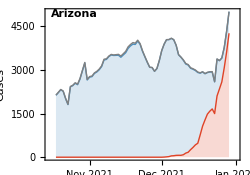
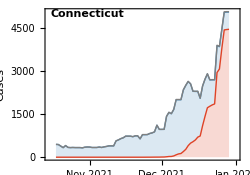
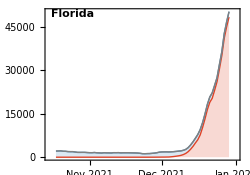
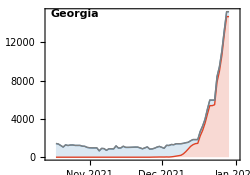
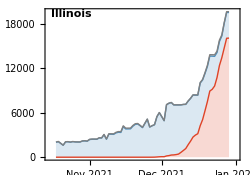
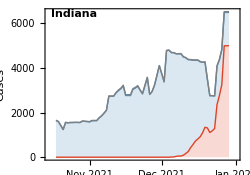
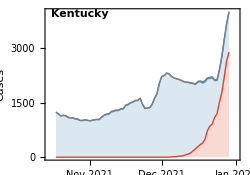
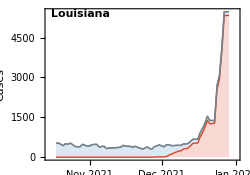
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=50000;
```

```mathematica
splitCaseLogPlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[state_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[state_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[state,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{20,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{1,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForStates=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,states];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{states,legendsForStates}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-log-cases.png